```mathematica
Table[{n,TriangularNumber[n]},{n,0,10}]
```

{{0,0},{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,28},{8,36},{9,45},{10,55}}

```mathematica
TableForm[
Table[
n->
Map[{TriangleNumber[n-1],Sum[
TriangleNumber[k-1],{k,#}]}&,IntegerPartitions[n,{4}]],{n,4,20}]
]
```

4→{{6,0}}
5→{{10,1}}
6→{{15,3},{15,2}}
7→{{21,6},{21,4},{21,3}}
8→{{28,10},{28,7},{28,6},{28,5},{28,4}}
9→{{36,15},{36,11},{36,9},{36,8},{36,7},{36,6}}
10→{{45,21},{45,16},{45,13},{45,12},{45,12},{45,10},{45,9},{45,9},{45,8}}
11→{{55,28},{55,22},{55,18},{55,17},{55,16},{55,14},{55,13},{55,13},{55,12},{55,11},{55,10}}
12→{{66,36},{66,29},{66,24},{66,23},{66,21},{66,19},{66,18},{66,20},{66,17},{66,16},{66,15},{66,15},{66,14},{66,13},{66,12}}
13→{{78,45},{78,37},{78,31},{78,30},{78,27},{78,25},{78,24},{78,25},{78,22},{78,21},{78,20},{78,21},{78,19},{78,18},{78,17},{78,18},{78,16},{78,15}}
14→{{91,55},{91,46},{91,39},{91,38},{91,34},{91,32},{91,31},{91,31},{91,28},{91,27},{91,26},{91,30},{91,26},{91,24},{91,23},{91,22},{91,23},{91,22},{91,22},{91,20},{91,19},{91,19},{91,18}}
15→{{105,66},{105,56},{105,48},{105,47},{105,42},{105,40},{105,39},{105,38},{105,35},{105,34},{105,33},{105,36},{105,32},{105,30},{105,29},{105,28},{105,31},{105,28},{105,27},{105,27},{105,25},{105,24},{105,26},{105,24},{105,23},{105,22},{105,21}}
16→{{120,78},{120,67},{120,58},{120,57},{120,51},{120,49},{120,48},{120,46},{120,43},{120,42},{120,41},{120,43},{120,39},{120,37},{120,36},{120,35},{120,42},{120,37},{120,34},{120,33},{120,33},{120,31},{120,30},{120,33},{120,32},{120,31},{120,29},{120,28},{120,27},{120,30},{120,27},{120,26},{120,25},{120,24}}
17→{{136,91},{136,79},{136,69},{136,68},{136,61},{136,59},{136,58},{136,55},{136,52},{136,51},{136,50},{136,51},{136,47},{136,45},{136,44},{136,43},{136,49},{136,44},{136,41},{136,40},{136,40},{136,38},{136,37},{136,43},{136,39},{136,38},{136,37},{136,35},{136,34},{136,33},{136,36},{136,34},{136,35},{136,32},{136,31},{136,30},{136,31},{136,29},{136,28}}
18→{{153,105},{153,92},{153,81},{153,80},{153,72},{153,70},{153,69},{153,65},{153,62},{153,61},{153,60},{153,60},{153,56},{153,54},{153,53},{153,52},{153,57},{153,52},{153,49},{153,48},{153,48},{153,46},{153,45},{153,56},{153,50},{153,46},{153,45},{153,44},{153,42},{153,41},{153,40},{153,45},{153,44},{153,42},{153,40},{153,41},{153,38},{153,37},{153,36},{153,40},{153,37},{153,36},{153,36},{153,34},{153,33},{153,33},{153,32}}
19→{{171,120},{171,106},{171,94},{171,93},{171,84},{171,82},{171,81},{171,76},{171,73},{171,72},{171,71},{171,70},{171,66},{171,64},{171,63},{171,62},{171,66},{171,61},{171,58},{171,57},{171,57},{171,55},{171,54},{171,64},{171,58},{171,54},{171,53},{171,52},{171,50},{171,49},{171,48},{171,57},{171,52},{171,51},{171,49},{171,47},{171,48},{171,45},{171,44},{171,43},{171,48},{171,46},{171,46},{171,43},{171,42},{171,42},{171,40},{171,39},{171,45},{171,41},{171,39},{171,38},{171,37},{171,36}}
20→{{190,136},{190,121},{190,108},{190,107},{190,97},{190,95},{190,94},{190,88},{190,85},{190,84},{190,83},{190,81},{190,77},{190,75},{190,74},{190,73},{190,76},{190,71},{190,68},{190,67},{190,67},{190,65},{190,64},{190,73},{190,67},{190,63},{190,62},{190,61},{190,59},{190,58},{190,57},{190,72},{190,65},{190,60},{190,59},{190,57},{190,55},{190,56},{190,53},{190,52},{190,51},{190,59},{190,58},{190,55},{190,53},{190,53},{190,50},{190,49},{190,49},{190,47},{190,46},{190,52},{190,49},{190,48},{190,51},{190,47},{190,45},{190,44},{190,43},{190,46},{190,43},{190,42},{190,41},{190,40}}

```mathematica
TableForm[
Table[
{n,3n-6}->
Map[TriangleNumber[n-1]-Sum[
TriangleNumber[k-1],{k,#}]&,IntegerPartitions[n,{4}]],{n,4,20}]
]
```

{4,6}→{6}
{5,9}→{9}
{6,12}→{12,13}
{7,15}→{15,17,18}
{8,18}→{18,21,22,23,24}
{9,21}→{21,25,27,28,29,30}
{10,24}→{24,29,32,33,33,35,36,36,37}
{11,27}→{27,33,37,38,39,41,42,42,43,44,45}
{12,30}→{30,37,42,43,45,47,48,46,49,50,51,51,52,53,54}
{13,33}→{33,41,47,48,51,53,54,53,56,57,58,57,59,60,61,60,62,63}
{14,36}→{36,45,52,53,57,59,60,60,63,64,65,61,65,67,68,69,68,69,69,71,72,72,73}
{15,39}→{39,49,57,58,63,65,66,67,70,71,72,69,73,75,76,77,74,77,78,78,80,81,79,81,82,83,84}
{16,42}→{42,53,62,63,69,71,72,74,77,78,79,77,81,83,84,85,78,83,86,87,87,89,90,87,88,89,91,92,93,90,93,94,95,96}
{17,45}→{45,57,67,68,75,77,78,81,84,85,86,85,89,91,92,93,87,92,95,96,96,98,99,93,97,98,99,101,102,103,100,102,101,104,105,106,105,107,108}
{18,48}→{48,61,72,73,81,83,84,88,91,92,93,93,97,99,100,101,96,101,104,105,105,107,108,97,103,107,108,109,111,112,113,108,109,111,113,112,115,116,117,113,116,117,117,119,120,120,121}
{19,51}→{51,65,77,78,87,89,90,95,98,99,100,101,105,107,108,109,105,110,113,114,114,116,117,107,113,117,118,119,121,122,123,114,119,120,122,124,123,126,127,128,123,125,125,128,129,129,131,132,126,130,132,133,134,135}
{20,54}→{54,69,82,83,93,95,96,102,105,106,107,109,113,115,116,117,114,119,122,123,123,125,126,117,123,127,128,129,131,132,133,118,125,130,131,133,135,134,137,138,139,131,132,135,137,137,140,141,141,143,144,138,141,142,139,143,145,146,147,144,147,148,149,150}

```mathematica
pl6=Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},MaximalPlanarQ[g]&&VertexCount[g]==6]&]
```

{7174416,7174414,7174368,7174360,7174342,7174336,7174206,7174200,7174182,7174174,7174128,7174126,7173714,7173712,7173642,7173616,7173478,7173454,7172262,7172254,7172238,7172158,7172014,7171942,7171534,7171528,7171510,7171456,7167888,7167882,7167862,7167802,7167622,7167568,7167162,7167154,7167136,7166920,7165704,7165702,7165624,7165462,7154742,7154740,7154688,7154680,7154524,7154518,7154040,7154038,7153960,7153798,7152582,7152574,7152556,7152340,7148206,7148200,7148182,7148128,7115394,7115392,7115322,7115296,7115158,7115134,7113216,7112974,7112488,7108840,7108762,7108114,7095712,7095694,7094992,6997302,6997294,6997278,6997198,6997054,6996982,6996576,6996334,6994390,6990736,6990718,6988558,6977620,6977542,6975436,6938254,6938248,6938230,6938176,6937528,6936070,6643008,6643002,6642982,6642922,6642742,6642688,6642280,6642202,6640816,6640798,6635722,6634264,6623328,6623086,6616768,6583962,6583954,6583936,6583720,6583234,6577402,6465864,6465862,6465784,6465622,6463678,6459304,5580102,5580100,5580048,5580040,5579884,5579878,5579392,5579374,5577940,5577862,5573568,5573326,5559718,5558260,5553886,5521080,5521078,5521000,5520838,5520352,5501398,5402982,5402974,5402956,5402740,5400796,5383300,5048686,5048680,5048662,5048608,5042128,5029006,2391448,2391400,2391240,2390754,2390752,2390728,2389296,2389288,2389216,2384920,2384914,2384680,2371774,2371720,2371558,2332434,2332432,2332408,2330248,2325874,2312752,2214336,2214328,2214256,2213608,2207776,2194654,1860040,1860034,1859800,1859314,1857856,1840360,797134,797080,796918,796432,794974,790600}

```mathematica
Tally[pl6,IsomorphicGraphQ[allGraphs6[#1,"graph"],allGraphs6[#2,"graph"]]&]
```

{{7174416,180},{7112974,15}}

```mathematica
ChromaticPolynomial[allGraphs6[7174416,"graph"],4]/24
```

1

```mathematica
ChromaticPolynomial[allGraphs6[7112974,"graph"],4]/24
```

4

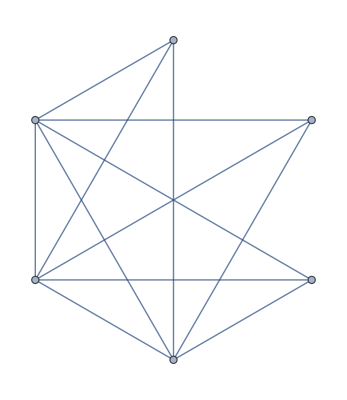
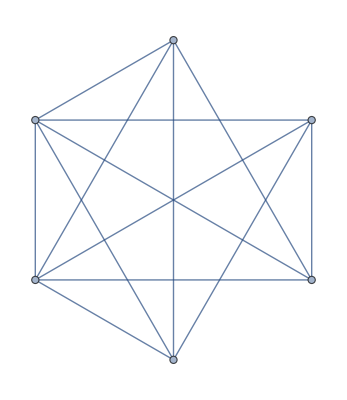

```mathematica
ListSols3[6]
```

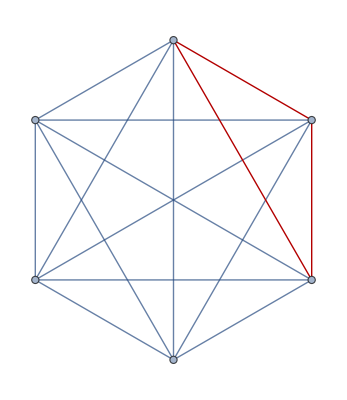

```mathematica
CompleteGraph[6,GraphHighlight->EdgeList[GraphComplement[-Graphics-]]]
```

```mathematica
ChromaticPolynomial[-Graphics-,4]/24
```

1

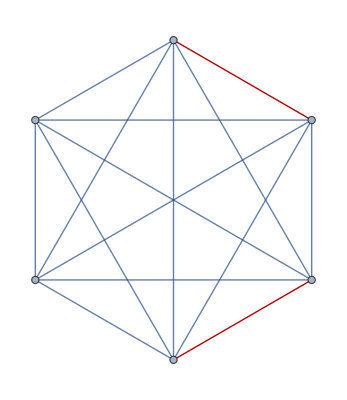

```mathematica
CompleteGraph[6,GraphHighlight->EdgeList[GraphComplement[-Graphics-]]]
```

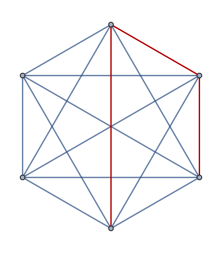

```mathematica
CompleteGraph[6,GraphHighlight->EdgeList[GraphComplement[allGraphs6[7174416,"graph"]]]]
```

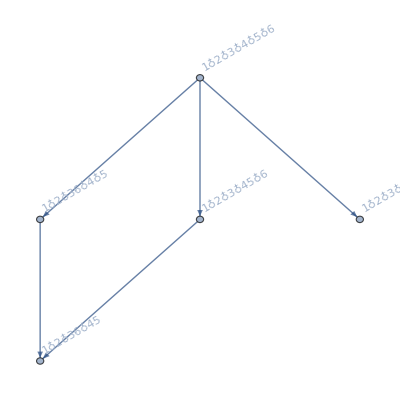

```mathematica
Graph[FormulaGraph2[ FindFullFormula[allGraphs6[7174416,"graph"]]],ImageSize->{500}]
```

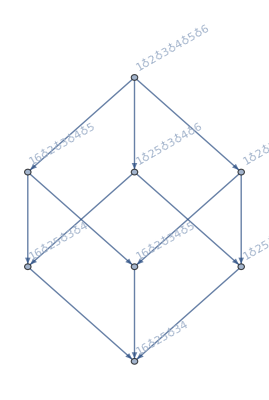

```mathematica
Graph[FormulaGraph2[ FindFullFormula[allGraphs6[7112974,"graph"]]],ImageSize->{500}]
```

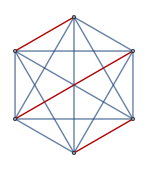

```mathematica
CompleteGraph[6,GraphHighlight->EdgeList[GraphComplement[allGraphs6[7112974,"graph"]]]]
```

```mathematica
TableForm[
Table[
n->
3n-6,{n,4,20}]
]
```

4→6
5→9
6→12
7→15
8→18
9→21
10→24
11→27
12→30
13→33
14→36
15→39
16→42
17→45
18→48
19→51
20→54

```mathematica
ListSols3[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{4}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
g=EdgeDelete[CompleteGraph[count],comp];
g
,
{part, parts}
]
]
```

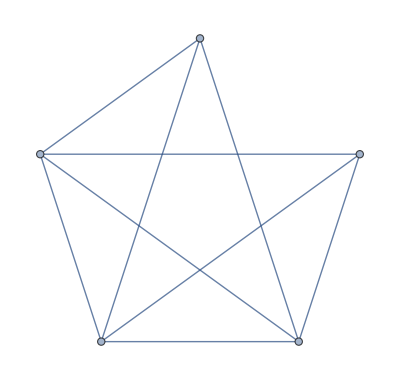
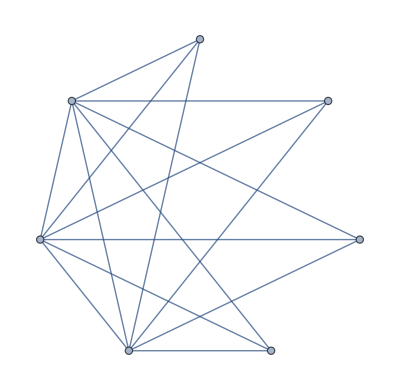
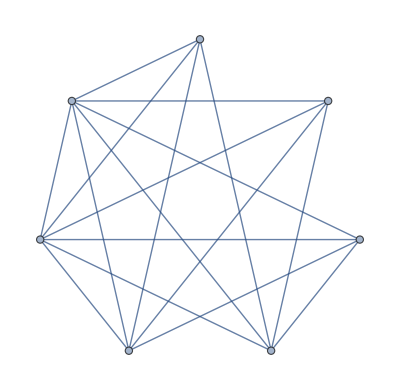
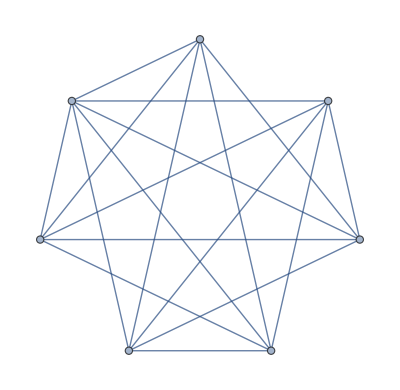
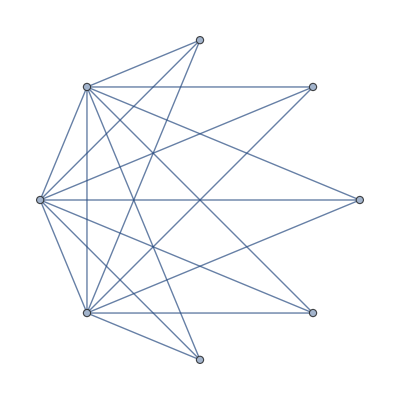
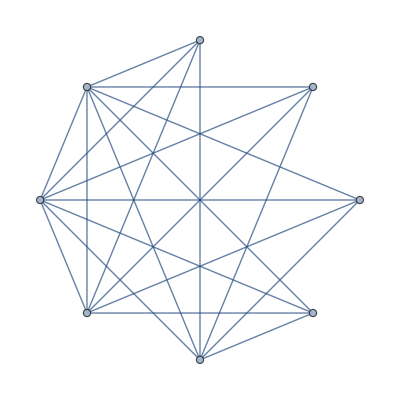
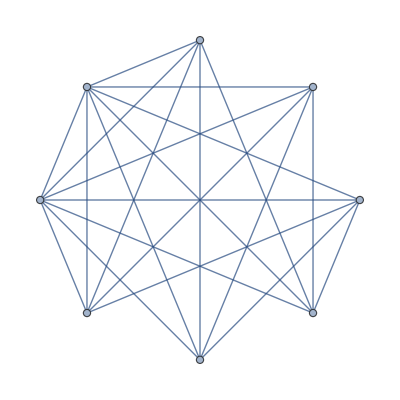
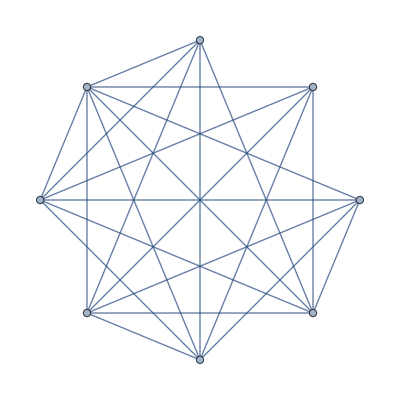
{-Graphics-{True,9}}
{-Graphics-{False,12},-Graphics-{False,13}}
{-Graphics-{False,15},-Graphics-{False,17},-Graphics-{False,18}}
{-Graphics-{False,18},-Graphics-{False,21},-Graphics-{False,22},-Graphics-{False,23},-Graphics-{False,24}}

```mathematica
Column[
Table[
With[{sol=ListSols3[max]},Map[Labeled[#,{PlanarGraphQ[#],EdgeCount[#]}]&,sol]],
{max,5,8}
]
]
```

```mathematica
EdgeCount[Graph[plantri[[1]]]]
```

30

```mathematica
VertexCount[Graph[plantri[[100]]]]
```

20

```mathematica
VertexCount[Graph[plantri[[1]]]]
```

12

```mathematica
f12=FindFullFormula[Graph[plantri[[1]]]]
```

```mathematica
Map[Map[Length,SymbolToSets[#]]&,Select[f12,StringCount[SymbolName[#],"x"]==3&]]
```

{{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3}}

```mathematica
IntegerPartitions[12,{4}]
```

{{9,1,1,1},{8,2,1,1},{7,3,1,1},{7,2,2,1},{6,4,1,1},{6,3,2,1},{6,2,2,2},{5,5,1,1},{5,4,2,1},{5,3,3,1},{5,3,2,2},{4,4,3,1},{4,4,2,2},{4,3,3,2},{3,3,3,3}}

```mathematica
With[{sol=ListSols3[6]},Map[Labeled[#,{PlanarGraphQ[#],EdgeCount[#]}]&,sol]]
```

{-Graphics-{False,12},-Graphics-{False,13}}

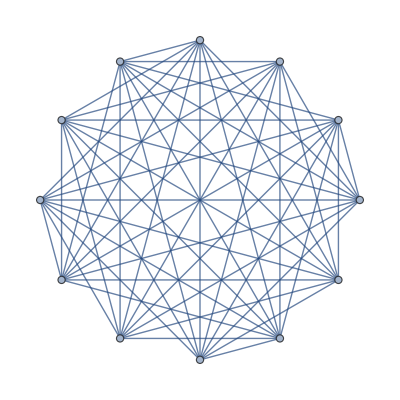
```mathematica
With[{g=-Graphics-},Table[VertexDegree[g,v],{v,VertexList[g]}]]
```

{9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
With[{g=Graph[plantri[[1]]]},Table[VertexDegree[g,v],{v,VertexList[g]}]]
```

{5,5,5,5,5,5,5,5,5,5,5,5}

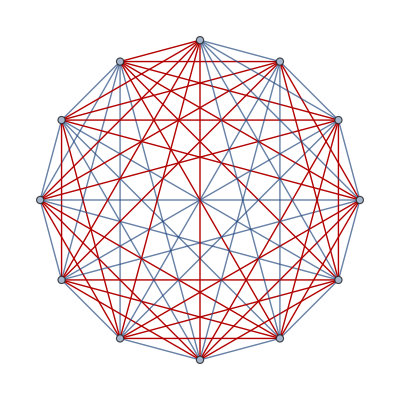

```mathematica
CompleteGraph[12,GraphHighlight->EdgeList[GraphComplement[Graph[plantri[[1]]]]]]
```